```mathematica
(*Quit[]*)
```

```mathematica
(*Import["/Users/conordyson/Documents/GitHub/BHPT/KerrGeodesics/KerrGeodesicsTest/Kernel/KerrGeoPlunge.m"]*)
```

```mathematica
(*SetDirectory@NotebookDirectory[];
PacletDirectoryLoad["."];
<<KerrGeodesics`*)
```

## Run This Section Before Testing

```mathematica
Off[Power::infy]
Off[Infinity::indet]
Off[FindRoot::brmp]
RPoly[λ_]:= (ϵ(r[λ]^2+a^2)-a*L)^2-(r[λ]^2-2*r[λ]+a^2)(r[λ]^2+(a*ϵ-L)^2+Q);
Polyθ[λ_] := (z[λ]^2-Z1^2)*(a^2(1-ϵ^2)z[λ]^2-Z2^2);
Polyϕ[λ_]:= a/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L) + L/(1-z[λ]^2)-a*ϵ;
TPoly[λ_]:=  (r[λ]^2+a^2)/((r[λ]-RP)(r[λ]-RM))(ϵ(r[λ]^2+a^2)-a*L)-a^2 ϵ(1-z[λ]^2)+a*L;
DN[a_] := (27-45 a^2+17 a^4+a^6+8 a^3 (1-a^2))^(1/3);
RISSOMIN[a_]:= 3+√(3+a^2+(9-10 a^2+a^4)/DN[a]+DN[a])-1/2 √(72+8 (-6+a^2)-(4 (9-10 a^2+a^4))/DN[a]-4 DN[a]+(64 a^2)/(√(3+a^2+(9-10 a^2+a^4)/DN[a]+DN[a])))

RISSOMAX[a_]:= 3+√(3+a^2+(9-10 a^2+a^4)/DN[a]+DN[a])+1/2 √(72+8 (-6+a^2)-(4 (9-10 a^2+a^4))/DN[a]-4 DN[a]+(64 a^2)/(√(3+a^2+(9-10 a^2+a^4)/DN[a]+DN[a])))
```

## ISSO Cases

### Random Cases

### ISSO Radial Param - No- IC

a=RandomReal[{0,1}];
λTest = RandomReal[{-1000,1000}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
RI = RandomReal[{RISSOMIN[a],RISSOMAX[a]}];
orbit=KerrGeoPlunge[a,"ISSORadialParam",RI ];
{t,r,θ,ϕ}  =orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
{Z1,Z2} = orbit["PolarRoots"];
z[y_] := Cos[θ[y]];
Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-10]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

### ISSO Radial Param - With- IC

a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
RI = RandomReal[{RISSOMIN[a],RISSOMAX[a]}];
{Z1,Z2} =KerrGeoPlunge[a,"ISSORadialParam",RI]["PolarRoots"];
t0 = RandomReal[{-1000,1000}];
r0 = RandomReal[{KerrGeoPlunge[a,"ISSORadialParam",RI]["RadialRoots"][[4]],RI}];
θ0 =RandomReal[{ArcCos[Z1],π-ArcCos[Z1]}];
 ϕ0=RandomReal[{-1000,1000}];
(*{RI,R4} = KerrGeoPlunge[a,"ISSORadialParam",6]["RadialRoots"][[3;;4]]*)
orbit=KerrGeoPlunge[a,"ISSORadialParam",RI,{t0 ,r0,θ0, ϕ0}];
{t,r,θ,ϕ}  =orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
{Z1,Z2} = orbit["PolarRoots"];
z[y_] := Cos[θ[y]];
Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-10]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

### ISSO Radial Param -ExtremalCase

a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
RI =RISSOMAX[a];
{Z1,Z2} =KerrGeoPlunge[a,"ISSORadialParam",RI]["PolarRoots"];
t0 = RandomReal[{-1000,1000}];
r0 = RandomReal[{KerrGeoPlunge[a,"ISSORadialParam",RI]["RadialRoots"][[4]],RI}];
θ0 =RandomReal[{ArcCos[Z1],π-ArcCos[Z1]}];
 ϕ0=RandomReal[{-1000,1000}];
(*{RI,R4} = KerrGeoPlunge[a,"ISSORadialParam",6]["RadialRoots"][[3;;4]]*)
orbit=KerrGeoPlunge[a,"ISSORadialParam",RI,{t0 ,r0,θ0, ϕ0}];
{t,r,θ,ϕ}  =orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
{Z1,Z2} = orbit["PolarRoots"];
z[y_] := Cos[θ[y]];
Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-10]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

### ISSO InclinedParam

a=RandomReal[{0,1}];
λTest = RandomReal[{-1000,1000}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
θINC = RandomReal[{-π/2,π/2}];
orbit=KerrGeoPlunge[a,"ISSOIncParam",θINC  ];
{t,r,θ,ϕ}  =orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
{Z1,Z2} = orbit["PolarRoots"];
z[y_] := Cos[θ[y]];
Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-10]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

### ISSO Radial Param - With- IC

a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
θINC = RandomReal[{-π/2,π/2}];
{Z1,Z2} =KerrGeoPlunge[a,"ISSOIncParam",θINC ]["PolarRoots"];
RI =KerrGeoPlunge[a,"ISSOIncParam",θINC ]["RadialRoots"][[3]];
R4= KerrGeoPlunge[a,"ISSOIncParam",θINC ]["RadialRoots"][[4]];
t0 = RandomReal[{-1000,1000}];
r0 = RandomReal[{R4,RI}];
θ0 =RandomReal[{ArcCos[Z1],π-ArcCos[Z1]}];
 ϕ0=RandomReal[{-1000,1000}];
orbit=KerrGeoPlunge[a,"ISSOIncParam",θINC,{t0 ,r0,θ0, ϕ0}];
{t,r,θ,ϕ}  =orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
z[y_] := Cos[θ[y]];
Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-10]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

### ISSO Inc Param -ExtremalCase

a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
θINC =- π/2;
{Z1,Z2} =KerrGeoPlunge[a,"ISSOIncParam",θINC ]["PolarRoots"];
RI =KerrGeoPlunge[a,"ISSOIncParam",θINC ]["RadialRoots"][[3]];
R4= KerrGeoPlunge[a,"ISSOIncParam",θINC ]["RadialRoots"][[4]];
t0 = RandomReal[{-1000,1000}];
r0 = RandomReal[{R4,RI}];
θ0 =RandomReal[{ArcCos[Z1],π-ArcCos[Z1]}];
 ϕ0=RandomReal[{-1000,1000}];
orbit=KerrGeoPlunge[a,"ISSOIncParam",θINC,{t0 ,r0,θ0, ϕ0}];
{t,r,θ,ϕ}  =orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
z[y_] := Cos[θ[y]];
Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-10]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

## Generic Cases

Example Parameters for 4 Real roots 3 of which outside r_+
		a =0.1;
		ϵ = 0.956;
		L =2.55;
		Q =6.54;
Example Parameters for 4 Real roots 3 of which Inside r_-
		a = 0.987;
		ϵ = 0.101;
		L = 0.39;
		Q = 1.×10^-8;

#### Without ICs

a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
ϵ =RandomReal[{0,1}];
L =RandomReal[{0,15}];
Q =RandomReal[{0,10}];
M=1;
orbit = KerrGeoPlunge[a,{ϵ,L,Q}];
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
z[λ_]:= Cos[θ[λ]];

Re[Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-8]]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

#### With ICs

a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
ϵ =RandomReal[{0,1}];
L =RandomReal[{0,15}];
Q =RandomReal[{0,10}];
M=1;
orbit = KerrGeoPlunge[a,{ϵ,L,Q}];
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
z[λ_]:= Cos[θ[λ]];

Re[Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-8]]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

#### With ICs

a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
ϵ =RandomReal[{0,1}];
L =RandomReal[{0,15}];
Q =RandomReal[{0,10}];
M=1;
R1 = KerrGeoPlunge[a,{ϵ,L,Q}]["RadialRoots"][[1]];
R2 = KerrGeoPlunge[a,{ϵ,L,Q}]["RadialRoots"][[2]];
{Z1,Z2} =KerrGeoPlunge[a,{ϵ,L,Q}]["PolarRoots"];
t0 = RandomReal[{-1000,1000}];
r0 = RandomReal[{R1,R2}];
θ0 =RandomReal[{ArcCos[Z1],π-ArcCos[Z1]}];
 ϕ0=RandomReal[{-1000,1000}];
(*{RI,R4} = KerrGeoPlunge[a,"ISSORadialParam",6]["RadialRoots"][[3;;4]]*)
orbit=KerrGeoPlunge[a,{ϵ,L,Q},{t0 ,r0,θ0, ϕ0}];
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"];
z[λ_]:= Cos[θ[λ]];

Re[Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-10]]

{0,0,0,0}

|  | "" |  | "»"

|  | "" | "" |

## Explicit Plotting

{0.377549,10.9974,8.2275}

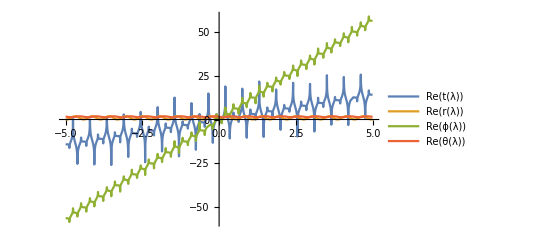

```mathematica
a=RandomReal[{0,1}];
RP = 1+Sqrt[1-a^2];
RM = 1-Sqrt[1-a^2];
ϵ =RandomReal[{0,1}];
L =RandomReal[{0,15}];
Q =RandomReal[{0,10}];
M=1;
orbit = KerrGeoPlunge[a,{ϵ,L,Q}];
{Z1,Z2}=orbit["PolarRoots"];
{t,r,θ,ϕ} = orbit["Trajectory"];
{ϵ,L,Q} = {"ℰ","ℒ" ,"𝒬"}/.orbit["ConstantsOfMotion"]
z[λ_]:= Cos[θ[λ]];
Re[Round[({t'[λ] - TPoly[λ],(r'[λ])^2-RPoly[λ] ,(-Sin[θ[λ]]θ'[λ])^2- Polyθ[λ], ϕ'[λ]-Polyϕ[λ]})/.λ->λTest, 10^-8]];
Plot[{Re[t[λ]],Re[ r[λ]],Re[ ϕ[λ]],Re[θ[λ]]},{λ,-5,5},PlotLegends->"Expressions", PlotRange->All]
(*Plot[{Re[RPoly[λ]], Re[(r'[λ])^2],Re[ (r'[λ])^2- RPoly[λ]]},{λ,-10,10}, PlotLegends->{RP1,RPrime,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{(z'[λ])^2, Polyθ[λ], (z'[λ])^2- Polyθ[λ]}, {λ,-10,10}, PlotLegends->Automatic ,PlotLegends->{PolyθQ,θQ,θQ-PolyθQ},  PlotRange->{{-10,10},{-0.0000000001,0.0000000001}}]
Plot[{Re[Polyϕ[λ]],Re[ϕ'[λ]],Re[ϕ'[λ]-Polyϕ[λ]]},{λ,-10,10},PlotLegends->{Polyϕ,ϕPrime,ϕPrime-Polyϕ},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]
Plot[{Re[t'[λ]],Re[ TPoly[λ] ], Re[t'[λ]- TPoly[λ]]},{λ,-10,10},PlotLegends->{TPRIME,TPLOY,Diff},  PlotRange->{{-10,10},{-0.000000001,0.000000001}}]*)
```